Testing of my  IntervalTools package.

```mathematica
<<IntervalTools`
NotebookDirectory[]
```

/Users/kevin/Dropbox/Research/Math Projects/AutomatedInequalities/

## Example 1: a polynomial in 1 variable (using multiple representations)

```mathematica
f[x_]=(x-1)(x-3)(x^2+2)+7;
gapF[x_]=Expand[f[x]]
```

13-8 x+5 x^2-4 x^3+x^4

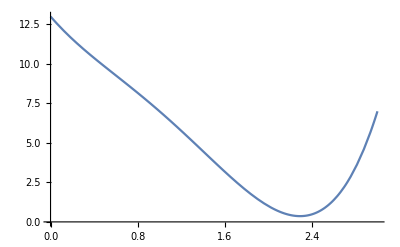

```mathematica
Plot[f[x],{x,0,3}]
```

```mathematica
ProveNonNegative[f,gapF,{Interval[{2,3}]}]
```

{{},{},{{Interval[{2,129/64}]},{Interval[{129/64,65/32}]},{Interval[{65/32,261/128}]},{Interval[{261/128,131/64}]},{Interval[{131/64,263/128}]},{Interval[{263/128,33/16}]},{Interval[{33/16,265/128}]},{Interval[{265/128,133/64}]},{Interval[{133/64,267/128}]},{Interval[{267/128,67/32}]},{Interval[{67/32,269/128}]},{Interval[{269/128,135/64}]},{Interval[{135/64,271/128}]},{Interval[{271/128,17/8}]},{Interval[{17/8,273/128}]},{Interval[{273/128,137/64}]},{Interval[{137/64,275/128}]},{Interval[{275/128,69/32}]},{Interval[{69/32,277/128}]},{Interval[{277/128,555/256}]},{Interval[{555/256,139/64}]},{Interval[{139/64,557/256}]},{Interval[{557/256,279/128}]},{Interval[{279/128,559/256}]},{Interval[{559/256,35/16}]},{Interval[{35/16,561/256}]},{Interval[{561/256,281/128}]},{Interval[{281/128,563/256}]},{Interval[{563/256,141/64}]},{Interval[{141/64,565/256}]},{Interval[{565/256,283/128}]},{Interval[{283/128,567/256}]},{Interval[{567/256,71/32}]},{Interval[{71/32,569/256}]},{Interval[{569/256,285/128}]},{Interval[{285/128,571/256}]},{Interval[{571/256,143/64}]},{Interval[{143/64,573/256}]},{Interval[{573/256,287/128}]},{Interval[{287/128,575/256}]},{Interval[{575/256,9/4}]},{Interval[{9/4,577/256}]},{Interval[{577/256,289/128}]},{Interval[{289/128,579/256}]},{Interval[{579/256,145/64}]},{Interval[{145/64,581/256}]},{Interval[{581/256,291/128}]},{Interval[{291/128,583/256}]},{Interval[{583/256,73/32}]},{Interval[{73/32,585/256}]},{Interval[{585/256,293/128}]},{Interval[{293/128,587/256}]},{Interval[{587/256,147/64}]},{Interval[{147/64,589/256}]},{Interval[{589/256,295/128}]},{Interval[{295/128,591/256}]},{Interval[{591/256,37/16}]},{Interval[{37/16,593/256}]},{Interval[{593/256,297/128}]},{Interval[{297/128,595/256}]},{Interval[{595/256,149/64}]},{Interval[{149/64,597/256}]},{Interval[{597/256,299/128}]},{Interval[{299/128,599/256}]},{Interval[{599/256,75/32}]},{Interval[{75/32,601/256}]},{Interval[{601/256,301/128}]},{Interval[{301/128,603/256}]},{Interval[{603/256,151/64}]},{Interval[{151/64,605/256}]},{Interval[{605/256,303/128}]},{Interval[{303/128,607/256}]},{Interval[{607/256,19/8}]},{Interval[{19/8,609/256}]},{Interval[{609/256,305/128}]},{Interval[{305/128,611/256}]},{Interval[{611/256,153/64}]},{Interval[{153/64,613/256}]},{Interval[{613/256,307/128}]},{Interval[{307/128,615/256}]},{Interval[{615/256,77/32}]},{Interval[{77/32,617/256}]},{Interval[{617/256,309/128}]},{Interval[{309/128,619/256}]},{Interval[{619/256,155/64}]},{Interval[{155/64,621/256}]},{Interval[{621/256,311/128}]},{Interval[{311/128,623/256}]},{Interval[{623/256,39/16}]},{Interval[{39/16,625/256}]},{Interval[{625/256,313/128}]},{Interval[{313/128,627/256}]},{Interval[{627/256,157/64}]},{Interval[{157/64,629/256}]},{Interval[{629/256,315/128}]},{Interval[{315/128,79/32}]},{Interval[{79/32,317/128}]},{Interval[{317/128,159/64}]},{Interval[{159/64,319/128}]},{Interval[{319/128,5/2}]},{Interval[{5/2,321/128}]},{Interval[{321/128,161/64}]},{Interval[{161/64,323/128}]},{Interval[{323/128,81/32}]},{Interval[{81/32,325/128}]},{Interval[{325/128,163/64}]},{Interval[{163/64,327/128}]},{Interval[{327/128,41/16}]},{Interval[{41/16,329/128}]},{Interval[{329/128,165/64}]},{Interval[{165/64,331/128}]},{Interval[{331/128,83/32}]},{Interval[{83/32,333/128}]},{Interval[{333/128,167/64}]},{Interval[{167/64,21/8}]},{Interval[{21/8,169/64}]},{Interval[{169/64,85/32}]},{Interval[{85/32,171/64}]},{Interval[{171/64,43/16}]},{Interval[{43/16,173/64}]},{Interval[{173/64,87/32}]},{Interval[{87/32,175/64}]},{Interval[{175/64,11/4}]},{Interval[{11/4,177/64}]},{Interval[{177/64,89/32}]},{Interval[{89/32,45/16}]},{Interval[{45/16,91/32}]},{Interval[{91/32,23/8}]},{Interval[{23/8,93/32}]},{Interval[{93/32,47/16}]},{Interval[{47/16,95/32}]},{Interval[{95/32,3}]}}}

```mathematica
Map[Length,%]
```

{0,0,132}

```mathematica
ProveNonNegative[f,gapF,{Interval[{-Infinity,Infinity}]},MaxDepth-> 12]
```

{{},{{Interval[{277/128,555/256}]},{Interval[{555/256,139/64}]},{Interval[{139/64,557/256}]},{Interval[{557/256,279/128}]},{Interval[{279/128,559/256}]},{Interval[{559/256,35/16}]},{Interval[{35/16,561/256}]},{Interval[{561/256,281/128}]},{Interval[{281/128,563/256}]},{Interval[{563/256,141/64}]},{Interval[{141/64,565/256}]},{Interval[{565/256,283/128}]},{Interval[{283/128,567/256}]},{Interval[{567/256,71/32}]},{Interval[{71/32,569/256}]},{Interval[{569/256,285/128}]},{Interval[{285/128,571/256}]},{Interval[{571/256,143/64}]},{Interval[{143/64,573/256}]},{Interval[{573/256,287/128}]},{Interval[{287/128,575/256}]},{Interval[{575/256,9/4}]},{Interval[{9/4,577/256}]},{Interval[{577/256,289/128}]},{Interval[{289/128,579/256}]},{Interval[{579/256,145/64}]},{Interval[{145/64,581/256}]},{Interval[{581/256,291/128}]},{Interval[{291/128,583/256}]},{Interval[{583/256,73/32}]},{Interval[{73/32,585/256}]},{Interval[{585/256,293/128}]},{Interval[{293/128,587/256}]},{Interval[{587/256,147/64}]},{Interval[{147/64,589/256}]},{Interval[{589/256,295/128}]},{Interval[{295/128,591/256}]},{Interval[{591/256,37/16}]},{Interval[{37/16,593/256}]},{Interval[{593/256,297/128}]},{Interval[{297/128,595/256}]},{Interval[{595/256,149/64}]},{Interval[{149/64,597/256}]},{Interval[{597/256,299/128}]},{Interval[{299/128,599/256}]},{Interval[{599/256,75/32}]},{Interval[{75/32,601/256}]},{Interval[{601/256,301/128}]},{Interval[{301/128,603/256}]},{Interval[{603/256,151/64}]},{Interval[{151/64,605/256}]},{Interval[{605/256,303/128}]},{Interval[{303/128,607/256}]},{Interval[{607/256,19/8}]},{Interval[{19/8,609/256}]},{Interval[{609/256,305/128}]},{Interval[{305/128,611/256}]},{Interval[{611/256,153/64}]},{Interval[{153/64,613/256}]},{Interval[{613/256,307/128}]},{Interval[{307/128,615/256}]},{Interval[{615/256,77/32}]},{Interval[{77/32,617/256}]},{Interval[{617/256,309/128}]},{Interval[{309/128,619/256}]},{Interval[{619/256,155/64}]},{Interval[{155/64,621/256}]},{Interval[{621/256,311/128}]},{Interval[{311/128,623/256}]},{Interval[{623/256,39/16}]},{Interval[{39/16,625/256}]},{Interval[{625/256,313/128}]},{Interval[{313/128,627/256}]},{Interval[{627/256,157/64}]},{Interval[{157/64,629/256}]},{Interval[{629/256,315/128}]},{Interval[{1024,2048}]},{Interval[{2048,∞}]}},{{Interval[{-∞,0}]},{Interval[{0,1}]},{Interval[{1,5/4}]},{Interval[{5/4,11/8}]},{Interval[{11/8,3/2}]},{Interval[{3/2,25/16}]},{Interval[{25/16,13/8}]},{Interval[{13/8,27/16}]},{Interval[{27/16,55/32}]},{Interval[{55/32,7/4}]},{Interval[{7/4,57/32}]},{Interval[{57/32,29/16}]},{Interval[{29/16,59/32}]},{Interval[{59/32,15/8}]},{Interval[{15/8,121/64}]},{Interval[{121/64,61/32}]},{Interval[{61/32,123/64}]},{Interval[{123/64,31/16}]},{Interval[{31/16,125/64}]},{Interval[{125/64,63/32}]},{Interval[{63/32,127/64}]},{Interval[{127/64,2}]},{Interval[{2,129/64}]},{Interval[{129/64,65/32}]},{Interval[{65/32,261/128}]},{Interval[{261/128,131/64}]},{Interval[{131/64,263/128}]},{Interval[{263/128,33/16}]},{Interval[{33/16,265/128}]},{Interval[{265/128,133/64}]},{Interval[{133/64,267/128}]},{Interval[{267/128,67/32}]},{Interval[{67/32,269/128}]},{Interval[{269/128,135/64}]},{Interval[{135/64,271/128}]},{Interval[{271/128,17/8}]},{Interval[{17/8,273/128}]},{Interval[{273/128,137/64}]},{Interval[{137/64,275/128}]},{Interval[{275/128,69/32}]},{Interval[{69/32,277/128}]},{Interval[{315/128,79/32}]},{Interval[{79/32,317/128}]},{Interval[{317/128,159/64}]},{Interval[{159/64,319/128}]},{Interval[{319/128,5/2}]},{Interval[{5/2,321/128}]},{Interval[{321/128,161/64}]},{Interval[{161/64,323/128}]},{Interval[{323/128,81/32}]},{Interval[{81/32,325/128}]},{Interval[{325/128,163/64}]},{Interval[{163/64,327/128}]},{Interval[{327/128,41/16}]},{Interval[{41/16,329/128}]},{Interval[{329/128,165/64}]},{Interval[{165/64,331/128}]},{Interval[{331/128,83/32}]},{Interval[{83/32,333/128}]},{Interval[{333/128,167/64}]},{Interval[{167/64,21/8}]},{Interval[{21/8,169/64}]},{Interval[{169/64,85/32}]},{Interval[{85/32,171/64}]},{Interval[{171/64,43/16}]},{Interval[{43/16,173/64}]},{Interval[{173/64,87/32}]},{Interval[{87/32,175/64}]},{Interval[{175/64,11/4}]},{Interval[{11/4,177/64}]},{Interval[{177/64,89/32}]},{Interval[{89/32,45/16}]},{Interval[{45/16,91/32}]},{Interval[{91/32,23/8}]},{Interval[{23/8,93/32}]},{Interval[{93/32,47/16}]},{Interval[{47/16,95/32}]},{Interval[{95/32,3}]},{Interval[{3,97/32}]},{Interval[{97/32,49/16}]},{Interval[{49/16,25/8}]},{Interval[{25/8,51/16}]},{Interval[{51/16,13/4}]},{Interval[{13/4,53/16}]},{Interval[{53/16,27/8}]},{Interval[{27/8,7/2}]},{Interval[{7/2,29/8}]},{Interval[{29/8,15/4}]},{Interval[{15/4,31/8}]},{Interval[{31/8,4}]},{Interval[{4,17/4}]},{Interval[{17/4,9/2}]},{Interval[{9/2,19/4}]},{Interval[{19/4,5}]},{Interval[{5,11/2}]},{Interval[{11/2,6}]},{Interval[{6,7}]},{Interval[{7,8}]},{Interval[{8,10}]},{Interval[{10,12}]},{Interval[{12,16}]},{Interval[{16,24}]},{Interval[{24,32}]},{Interval[{32,64}]},{Interval[{64,128}]},{Interval[{128,256}]},{Interval[{256,512}]},{Interval[{512,1024}]}}}

```mathematica
Map[Length,%]
```

{0,78,108}

```mathematica
gapF[x_]:=IntervalIntersection[7+(-3+x) (-1+x) (2+x^2),13-8 x+5 x^2-4 x^3+x^4]
```

```mathematica
ProveNonNegative[f,gapF,{Interval[{-Infinity,Infinity}]},MaxDepth->12]
```

{{},{},{{Interval[{-∞,0}]},{Interval[{0,1}]},{Interval[{1,3/2}]},{Interval[{3/2,7/4}]},{Interval[{7/4,15/8}]},{Interval[{15/8,2}]},{Interval[{2,33/16}]},{Interval[{33/16,17/8}]},{Interval[{17/8,69/32}]},{Interval[{69/32,35/16}]},{Interval[{35/16,71/32}]},{Interval[{71/32,9/4}]},{Interval[{9/4,73/32}]},{Interval[{73/32,37/16}]},{Interval[{37/16,75/32}]},{Interval[{75/32,19/8}]},{Interval[{19/8,77/32}]},{Interval[{77/32,39/16}]},{Interval[{39/16,5/2}]},{Interval[{5/2,41/16}]},{Interval[{41/16,21/8}]},{Interval[{21/8,11/4}]},{Interval[{11/4,3}]},{Interval[{3,4}]},{Interval[{4,∞}]}}}

## Example 2: an involved function of 2 variables (50 seconds)

```mathematica
f[x_,y_]=-2/37+ArcTan[x^2+2 y^2-Sin[x]]+(2+Sin[x+y])/(ⅇ^(-2 x)+ⅇ^x+ⅇ^(1-y)+3 ⅇ^(5 y));
FindMinimum[f[x,y],{x,y}]
```

{0.00028027,{x→0.422893,y→0.150277}}

If a function is not too involved, such as this one, it can serve as its own enclosure.

```mathematica
RealInterval=Interval[{-Infinity,Infinity}];
```

```mathematica
AbsoluteTiming[cert=ProveNonNegative[f,f,{RealInterval,RealInterval}];]
Map[Length,cert]
```

{3.04165,Null}

{0,892,1884}

In other words, the algorithm found 0 places where f is definitely negative, 1884 subdomains where f is definitely positive, and was unable to reach a conclusion on 892 subdomains.

In two dimensions, we can picture the subdomains returned by ProveNonNegative with the IntervalGraphics command. We first have to make them bounded, though.

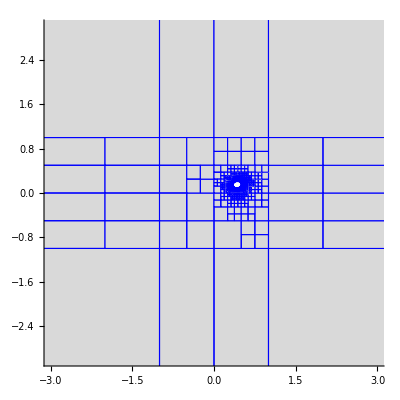

```mathematica
Show[IntervalGraphics[cert⟦3⟧/.{-∞->-4,∞->4},{Interval[{-3,3}],Interval[{-3,3}]}],Axes->True]
```

One sees the algorithm using smaller boxes close when f gets close to 0, and the white “pimple” where the algorithm was undecided. To help the algorithm eliminate the white, we can think more about a better enclosing function, or we can allow the algorithm to inspect smaller subdomains with a MaxDepth option, which defaults to 10. The option “certificate -> False” would have the algorithm only return the most recent subdomain of each type. It is generally easier to allow the algorithm to use smaller subdomains, but faster to find a better enclosing function.

```mathematica
AbsoluteTiming[cert=ProveNonNegative[f,f,{RealInterval,RealInterval},MaxDepth->25];]
Map[Length,cert]
```

{47.428,Null}

{0,0,47803}

That is 0 undecided subdomains remaining. We have a proof of positivity!

```mathematica
Show[IntervalGraphics[cert⟦3⟧/.{-∞->-4,∞->4},{Interval[{-3,3}],Interval[{-3,3}]}],Axes->True]
```

-Graphics-